# Quintic splines

```mathematica
ClearAll["Global`*"]
```

This file explains the basic working of quintic splines, as we use them in the paper of Thomas Blanchet, Juliette Fournier and Thomas Piketty, “Generalized Pareto Curves: Theory and Applications”, 2017.

### Basis functions

Determine the basis functions by solving the appropriate linear system:

```mathematica
poly[x_]=Sum[Subscript[a, i] x^i,{i,0,5}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5

```mathematica
coef=CoefficientList[poly[x],x]
```

{a_0,a_1,a_2,a_3,a_4,a_5}

```mathematica
h00[x_]=poly[x]/.First[Solve[{poly[0]==1,poly[1]==0,poly'[0]==0,poly'[1]==0,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h01[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==1,poly'[0]==0,poly'[1]==0,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h10[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==1,poly'[1]==0,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h11[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==1,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h20[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==0,poly''[0]==1,poly''[1]==0},coef]];
```

```mathematica
h21[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==0,poly''[0]==0,poly''[1]==1},coef]];
```

Expressions of the basis functions:

```mathematica
TableForm[Map[#&,{h00[x],h01[x],h10[x],h11[x],h20[x],h21[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | 1-10 x^3+15 x^4-6 x^5
h01 | 10 x^3-15 x^4+6 x^5
h10 | x-6 x^3+8 x^4-3 x^5
h11 | -4 x^3+7 x^4-3 x^5
h20 | x^2/2-(3 x^3)/2+(3 x^4)/2-x^5/2
h21 | x^3/2-x^4+x^5/2

Their first derivatives:

```mathematica
TableForm[Map[D[#,x]&,{h00[x],h01[x],h10[x],h11[x],h20[x],h21[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | -30 x^2+60 x^3-30 x^4
h01 | 30 x^2-60 x^3+30 x^4
h10 | 1-18 x^2+32 x^3-15 x^4
h11 | -12 x^2+28 x^3-15 x^4
h20 | x-(9 x^2)/2+6 x^3-(5 x^4)/2
h21 | (3 x^2)/2-4 x^3+(5 x^4)/2

Their second derivatives:

```mathematica
TableForm[Map[D[#,{x,2}]&,{h00[x],h01[x],h10[x],h11[x],h20[x],h21[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | -60 x+180 x^2-120 x^3
h01 | 60 x-180 x^2+120 x^3
h10 | -36 x+96 x^2-60 x^3
h11 | -24 x+84 x^2-60 x^3
h20 | 1-9 x+18 x^2-10 x^3
h21 | 3 x-12 x^2+10 x^3

Their third derivatives:

```mathematica
TableForm[Map[D[#,{x,3}]&,{h00[x],h01[x],h10[x],h11[x],h20[x],h21[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | -60+360 x-360 x^2
h01 | 60-360 x+360 x^2
h10 | -36+192 x-180 x^2
h11 | -24+168 x-180 x^2
h20 | -9+36 x-30 x^2
h21 | 3-24 x+30 x^2

Plots of the basis functions:

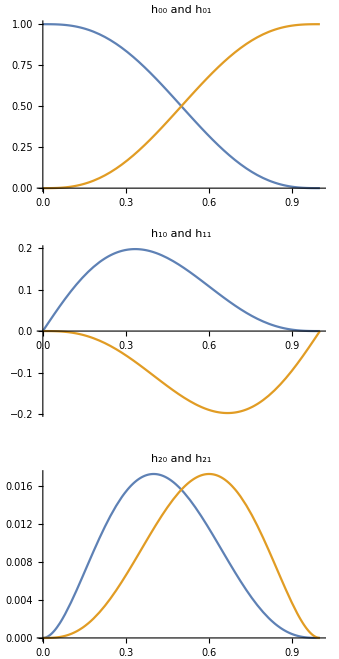

```mathematica
GraphicsColumn[{Plot[{h00[x],h01[x]},{x,0,1},PlotLabel->"h_00 and h_01"],Plot[{h10[x],h11[x]},{x,0,1},PlotLabel->"h_10 and h_11"],Plot[{h20[x],h21[x]},{x,0,1},PlotLabel->"h_20 and h_21"]}]
```

Their first derivatives:

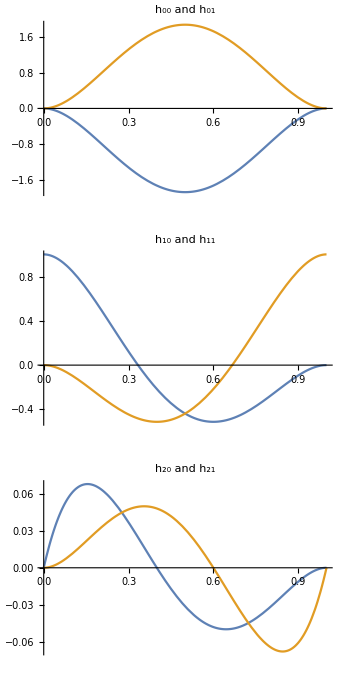

```mathematica
GraphicsColumn[{Plot[Evaluate[{h00'[x],h01'[x]}],{x,0,1},PlotLabel->"h_00 and h_01"],Plot[Evaluate[{h10'[x],h11'[x]}],{x,0,1},PlotLabel->"h_10 and h_11"],Plot[Evaluate[{h20'[x],h21'[x]}],{x,0,1},PlotLabel->"h_20 and h_21"]}]
```

Their second derivatives:

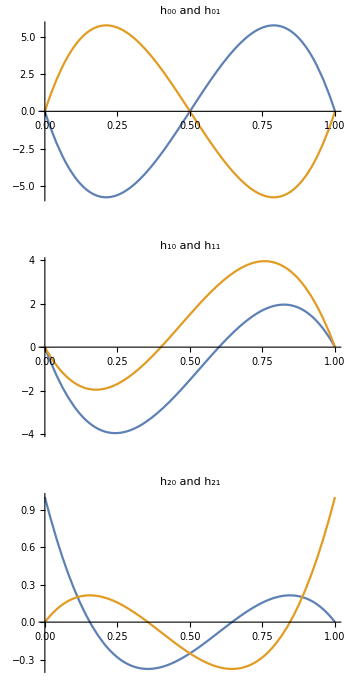

```mathematica
GraphicsColumn[{Plot[Evaluate[{h00''[x],h01''[x]}],{x,0,1},PlotLabel->"h_00 and h_01"],Plot[Evaluate[{h10''[x],h11''[x]}],{x,0,1},PlotLabel->"h_10 and h_11"],Plot[Evaluate[{h20''[x],h21''[x]}],{x,0,1},PlotLabel->"h_20 and h_21"]}]
```

### Interpolation function

The interpolating function over [0, 1] is a linear combination of those six basis functions:

```mathematica
h[x_,y0_,y1_,s0_,s1_,a0_,a1_]=y0*h00[x]+y1*h01[x]+s0*h10[x]+s1*h11[x]+a0*h20[x]+a1*h21[x];
```

```mathematica
Manipulate[GraphicsColumn[{Plot[h[x,y0,y1,s0,s1,a0,a1],{x,0,1},PlotRange->{{0,1},{-2,2}},PlotLabel->"Quintic spline function"],Plot[Evaluate[D[h[x,y0,y1,s0,s1,a0,a1],x]],{x,0,1},PlotRange->{{0,1},{-10,10}},PlotLabel->"First derivative"],Plot[Evaluate[D[h[x,y0,y1,s0,s1,a0,a1],{x,2}]],{x,0,1},PlotRange->{{0,1},{-50,50}},PlotLabel->"Second derivative"]}],{{y0,-1},-2,2},{{y1,1},-2,2},{{s0,0},-2,2},{{s1,0},-2,2},{{a0,0},-20,20},{{a1,0},-20,20}]
```

We can extend this function to an arbitrary interval using an affine transformation:

```mathematica
f[x_]=y0*h00[(x-x0)/(x1-x0)]+y1*h01[(x-x0)/(x1-x0)]+s0*(x1-x0)*h10[(x-x0)/(x1-x0)]+s1*(x1-x0)*h11[(x-x0)/(x1-x0)]+a0*(x1-x0)^2*h20[(x-x0)/(x1-x0)]+a1*(x1-x0)^2*h21[(x-x0)/(x1-x0)];
```

Check that the function and its derivatives have the right values:

```mathematica
{f[x0],f[x1],f'[x0],f'[x1],f''[x0],f''[x1]}
```

{y0,y1,s0,s1,a0,a1}

## Regularity conditions to determine the parameters of the spline

To determine the parameters of the spline, we impose the requirement that the third derivative is continuous at the jointures. That leads to the most regular curve possible in the sense that the first derivative has the lowest curvature possible.

We start by defining two splines over the knots (x_1,x_2,x_3). The spline over (x_1,x_2) if f_1, and the one over (x_2,x_3) is f_2.

```mathematica
f1[x_]=y1*h00[(x-x1)/(x2-x1)]+y2*h01[(x-x1)/(x2-x1)]+s1*(x2-x1)*h10[(x-x1)/(x2-x1)]+s2*(x2-x1)*h11[(x-x1)/(x2-x1)]+a1*(x2-x1)^2*h20[(x-x1)/(x2-x1)]+a2*(x2-x1)^2*h21[(x-x1)/(x2-x1)];
```

```mathematica
f2[x_]=y2*h00[(x-x2)/(x3-x2)]+y3*h01[(x-x2)/(x3-x2)]+s2*(x3-x2)*h10[(x-x2)/(x3-x2)]+s3*(x3-x2)*h11[(x-x2)/(x3-x2)]+a2*(x3-x2)^2*h20[(x-x2)/(x3-x2)]+a3*(x3-x2)^2*h21[(x-x2)/(x3-x2)];
```

Get the system in matrix form:

```mathematica
system=CoefficientArrays[{f1'''[x2]==f2'''[x2]},{a1,a2,a3}];
```

```mathematica
system[[1]]//Normal
```

{-(24 s1)/(-x1+x2)^2-(36 s2)/(-x1+x2)^2+(36 s2)/(-x2+x3)^2+(24 s3)/(-x2+x3)^2-(60 y1)/(-x1+x2)^3+(60 y2)/(-x1+x2)^3+(60 y2)/(-x2+x3)^3-(60 y3)/(-x2+x3)^3}

```mathematica
system[[2]]//Normal
```

{{-3/(-x1+x2),9/(-x1+x2)+9/(-x2+x3),-3/(-x2+x3)}}

We need two additional equations for the system to be uniquely determined. At the lower end (first knot), we impose the third derivative equal to zero.

```mathematica
systemfirst=CoefficientArrays[{f1'''[x1]==0},{a1,a2,a3}];
```

```mathematica
systemfirst[[1]]//Normal
```

{-(36 s1)/(-x1+x2)^2-(24 s2)/(-x1+x2)^2-(60 y1)/(-x1+x2)^3+(60 y2)/(-x1+x2)^3}

```mathematica
systemfirst[[2]]//Normal
```

{{-9/(-x1+x2),3/(-x1+x2),0}}

At the upper end (last knot), we estimate the second derivative directly using a two-points difference:

```mathematica
systemlast=CoefficientArrays[{f1''[x1]==(s3-s2)/(x3-x2)},{a1,a2,a3}];
```

```mathematica
systemlast[[1]]//Normal
```

{-(-s2+s3)/(-x2+x3)}

```mathematica
systemlast[[2]]//Normal
```

{{1,0,0}}

Calculate explicit solution for testing purposes:

```mathematica
Simplify[Solve[{f1'''[x2]==f2'''[x2],f1'''[x1]==0,f2''[x3]==(s3-s2)/(x3-x2)},{a1,a2,a3}]]//InputForm
```

{{a1 -> (7*s3*(x1 - x2)^3*(x2 - x3) + s2*(x1 - x2)*(x2 - x3)*(13*x1^2 + x2^2 + 12*x3^2 - 
       2*x1*(x2 + 12*x3)) + 4*(s1*(x1 - x2)*(9*x1 - 2*x2 - 7*x3)*(x2 - x3)^2 - 
       5*(3*x2*x3^2*(y1 - y2) + 2*x3^3*(-y1 + y2) + 3*x1*(x3^2*(y1 - y2) + 
           2*x2*x3*(-y1 + y2) + x2^2*(y1 - y3)) + x1^3*(y2 - y3) + x2^3*(-y1 + y3) + 
         3*x1^2*x2*(-y2 + y3))))/((x1 - x2)^2*(9*x1 - x2 - 8*x3)*(x2 - x3)^2), 
  a2 -> (21*s3*(x1 - x2)^3*(x2 - x3) + s2*(x1 - x2)*(x2 - x3)*
      (39*x1^2 - 78*x1*x2 + 11*x2^2 + 56*x2*x3 - 28*x3^2) - 
     4*(3*s1*(x1 - x2)*(x2 - x3)^3 - 5*(-2*x3^3*(y1 - y2) + 
         x2*(6*x3^2*(y1 - y2) + 9*x1^2*(y2 - y3)) + x2^3*(2*y1 + y2 - 3*y3) + 
         3*x1^3*(-y2 + y3) + x2^2*(-6*x3*y1 - 9*x1*y2 + 6*x3*y2 + 9*x1*y3))))/
    ((x1 - x2)^2*(9*x1 - x2 - 8*x3)*(x2 - x3)^2), a3 -> (s2 - s3)/(x2 - x3)}}

### Constraint on the spline

The interpolation method requires certain conditions on the spline to get a nondecreasing quantile function. We search for a lower bound of the polynomial f''(x_0+x(x_1-x_0))+f'(x_0+x(x_1-x_0))(1-f'(x_0+x(x_1-x_0))) over [0, 1].

```mathematica
g=f''[x0+x(x1-x0)]+f'[x0+x(x1-x0)](1-f'[x0+x(x1-x0)]);
```

```mathematica
gcoefs=Simplify[CoefficientList[g,x]];
```

We rewrite the polynomial in its Bernstein form:

```mathematica
tobernstein[k_]:=Sum[Part[gcoefs,r+1]*Binomial[k,r]/Binomial[Length[gcoefs]-1,r],{r,0,k}]
```

```mathematica
bernsteincoefs=FullSimplify[Map[tobernstein,Range[0,Length[gcoefs]-1]]];
```

Hence, we require all the following expressions to be non-negative:

```mathematica
TableForm[bernsteincoefs]
```

a0+s0-s0^2
a0+s0-s0^2+((x0-x1) (24 s1+2 s0 (18+a0 (x0-x1)^2)+(x0-x1) (3 a1+a0 (-9-x0+x1)))+60 (-y0+y1))/(8 (x0-x1)^2)
(-480 (y0-y1)+(x0-x1) (16 s0^2 (x0-x1)-(a0 (34+5 x0-5 x1)+3 a1 (-6+x0-x1)+2 a0^2 (x0-x1)^2) (x0-x1)+24 s1 (7-x0+x1)+60 (y0-y1)+2 s0 (156+(5 a0+3 a1) x0^2+2 x0 (5+12 s1-5 a0 x1-3 a1 x1)+x1 (-10-24 s1+5 a0 x1+3 a1 x1)-60 y0+60 y1)))/(56 (x0-x1)^2)
(-300 (y0-y1)+(x0-x1) (96 s0^2 (x0-x1)+4 s1 (15-6 a0 x0^2+x1 (11-6 a0 x1)+x0 (-11+12 a0 x1))+2 s0 ((-18 a0+5 a1) x0^2+2 x0 (-5+22 s1+18 a0 x1-5 a1 x1)+x1 (10-44 s1-18 a0 x1+5 a1 x1)-120 (-1+y0-y1))+120 (y0-y1)+(x0-x1) (a1-5 a1 x0+3 a0^2 (x0-x1)^2+5 a1 x1-a0 (35+3 a1 (x0-x1)^2-60 y0+60 y1))))/(56 (x0-x1)^2)
-(100 a0 x0^2+100 a1 x0^2-20 a0 x0^3+20 a1 x0^3+9 a0^2 x0^4-26 a0 a1 x0^4+9 a1^2 x0^4+576 s0^2 (x0-x1)^2+576 s1^2 (x0-x1)^2-200 a0 x0 x1-200 a1 x0 x1+60 a0 x0^2 x1-60 a1 x0^2 x1-36 a0^2 x0^3 x1+104 a0 a1 x0^3 x1-36 a1^2 x0^3 x1+100 a0 x1^2+100 a1 x1^2-60 a0 x0 x1^2+60 a1 x0 x1^2+54 a0^2 x0^2 x1^2-156 a0 a1 x0^2 x1^2+54 a1^2 x0^2 x1^2+20 a0 x1^3-20 a1 x1^3-36 a0^2 x0 x1^3+104 a0 a1 x0 x1^3-36 a1^2 x0 x1^3+9 a0^2 x1^4-26 a0 a1 x1^4+9 a1^2 x1^4-720 x0 y0+360 a0 x0^2 y0-360 a1 x0^2 y0+720 x1 y0-720 a0 x0 x1 y0+720 a1 x0 x1 y0+360 a0 x1^2 y0-360 a1 x1^2 y0+3600 y0^2-4 s1 (x0-x1) (4 (11 a0-9 a1) x0^2+x1 (55+44 a0 x1-36 a1 x1)+x0 (-55-88 a0 x1+72 a1 x1)+120 (-1+6 y0-6 y1))-4 s0 (x0-x1) (4 (9 a0-11 a1) x0^2-x0 (55+322 s1+72 a0 x1-88 a1 x1)+x1 (55+322 s1+36 a0 x1-44 a1 x1)+120 (1+6 y0-6 y1))-360 ((-2+(a0-a1) (x0-x1)) (x0-x1)+20 y0) y1+3600 y1^2)/(280 (x0-x1)^2)
((x0-x1) (96 s1^2 (x0-x1)+4 s0 (-15+6 a1 x0^2+x0 (-11+22 s1-12 a1 x1)+x1 (11-22 s1+6 a1 x1))-(x0-x1) (a0 (-1+x0 (-5+3 a1 x0)+5 x1-6 a1 x0 x1+3 a1 x1^2)+a1 (35-3 a1 (x0-x1)^2+60 y0-60 y1))-2 s1 ((5 a0-18 a1) x0^2+x1 (-10+5 a0 x1-18 a1 x1)+2 x0 (5-5 a0 x1+18 a1 x1)+120 (1+y0-y1))+120 (y0-y1))+300 (y0-y1))/(56 (x0-x1)^2)
(480 (y0-y1)-(x0-x1) ((34 a1+a1 (-5+2 a1 (x0-x1)) (x0-x1)-3 a0 (6+x0-x1)) (x0-x1)+16 s1^2 (-x0+x1)-24 s0 (-7+(-1+2 s1) x0+x1-2 s1 x1)+2 s1 ((3 a0+5 a1) x0^2-2 x0 (5+3 a0 x1+5 a1 x1)+x1 (10+3 a0 x1+5 a1 x1)+12 (13+5 y0-5 y1))+60 (-y0+y1)))/(56 (x0-x1)^2)
(-(x0-x1) (24 s0+8 s1^2 (x0-x1)-(3 a0+a1 (-1+x0-x1)) (x0-x1)+2 s1 (18+a1 x0^2-2 x0 (2+a1 x1)+x1 (4+a1 x1)))+60 (y0-y1))/(8 (x0-x1)^2)
a1+s1-s1^2

```mathematica
Map[InputForm[Simplify[D[#,a1]]]&,bernsteincoefs]//TableForm
```

0
3/8
(3*(6 + (-1 + 2*s0)*x0 + x1 - 2*s0*x1))/56
(1 - 3*a0*x0^2 + (5 - 10*s0)*x1 - 3*a0*x1^2 + x0*(-5 + 10*s0 + 6*a0*x1))/56
((13*a0 - 9*a1)*x0^2 + 2*(5 + 44*s0 + 36*s1)*x1 + (13*a0 - 9*a1)*x1^2 - 2*x0*(5 + 44*s0 + 36*s1 + 13*a0*x1 - 9*a1*x1) + 10*(-5 + 18*y0 - 18*y1))/140
(-35 - 3*a0*x0^2 + 6*a1*x0^2 + 24*s0*(x0 - x1) + 36*s1*(x0 - x1) + 6*a0*x0*x1 - 12*a1*x0*x1 - 3*a0*x1^2 + 6*a1*x1^2 - 60*y0 + 60*y1)/56
(-34 - 4*a1*x0^2 + 5*(-1 + 2*s1)*x1 - 4*a1*x1^2 + x0*(5 - 10*s1 + 8*a1*x1))/56
(-1 + x0 - 2*s1*x0 + (-1 + 2*s1)*x1)/8
1

```mathematica
ϕ[x_,x0_,x1_,y0_,y1_,s0_,s1_,a0_,a1_]=g;
```

```mathematica
ψ[x0_,x1_,y0_,y1_,s0_,s1_,a0_,a1_]=Min[bernsteincoefs];
```

We can check the bound for different values of the parameters.

```mathematica
Manipulate[Plot[{ϕ[x,0,1,y0,y1,s0,s1,a0,a1],ψ[0,1,y0,y1,s0,s1,a0,a1]},{x,0,1},PlotRange->{{0,1},{-2,2}},AspectRatio->1],{{y0,2},1,4},{{y1,2.5},1,4},{{s0,1/2},0,2},{{s1,1/2},0,2},{{a0,0},-10,10},{{a1,0},-10,10}]
```

```mathematica
Map[InputForm[Simplify[#]]&,CoefficientList[g,x]]//TableForm
```

a0 + s0 - s0^2
a0*(-9 + (-1 + 2*s0)*x0 + x1 - 2*s0*x1) + (3*(a1*x0^2 + 12*s0*(x0 - x1) + 8*s1*(x0 - x1) - 2*a1*x0*x1 + a1*x1^2 - 20*y0 + 20*y1))/(x0 - x1)^2
-(a0^2*(x0 - x1)^2) - (9*a0*(-4 + (-1 + 2*s0)*x0 + x1 - 2*s0*x1))/2 + (3*(a1*(-8 + (-1 + 2*s0)*x0 + x1 - 2*s0*x1) + (4*(6*s0^2*(x0 - x1)^2 - 2*s1*(x0^2 + x0*(7 - 2*x1) + (-7 + x1)*x1) + 5*(6 + x0 - x1)*(y0 - y1) + s0*(x0 - x1)*(-16 + (-3 + 4*s1)*x0 + 3*x1 - 4*s1*x1 - 10*y0 + 10*y1)))/(x0 - x1)^2))/2
9*a0^2*(x0 - x1)^2 - a0*(10 + 3*a1*x0^2 - 6*(1 + 4*s0 + 4*s1)*x1 + 3*a1*x1^2 + 6*x0*(1 + 4*s0 + 4*s1 - a1*x1) - 60*y0 + 60*y1) + 2*(a1*(5 + (2 - 4*s0)*x0 + (-2 + 4*s0)*x1) - (2*(16*s0^2*(x0 - x1)^2 + s1*(-7*x0^2 + (15 - 7*x1)*x1 + x0*(-15 + 14*x1)) + 15*(2 + x0 - x1)*(y0 - y1) + s0*(x0 - x1)*(-15 + 2*(-4 + 7*s1)*x0 + 8*x1 - 14*s1*x1 - 30*y0 + 30*y1)))/(x0 - x1)^2)
-15*s0 - 294*s0^2 - 15*s1 - 402*s0*s1 - 144*s1^2 + (5*a0*(x0 - x1))/2 + 221*a0*s0*(x0 - x1) + 164*a0*s1*(x0 - x1) - (129*a0^2*(x0 - x1)^2)/4 + (43*a0*a1*(x0 - x1)^2)/2 - (9*a1^2*(x0 - x1)^2)/4 + (5*a1*(-x0 + x1))/2 + 49*a1*s0*(-x0 + x1) + 36*a1*s1*(-x0 + x1) - 390*a0*y0 + 90*a1*y0 + (30*y0)/(x0 - x1) + (1020*s0*y0)/(x0 - x1) + (720*s1*y0)/(x0 - x1) - (900*y0^2)/(x0 - x1)^2 + 390*a0*y1 - 90*a1*y1 + (30*y1)/(-x0 + x1) + (1020*s0*y1)/(-x0 + x1) + (720*s1*y1)/(-x0 + x1) + (1800*y0*y1)/(x0 - x1)^2 - (900*y1^2)/(x0 - x1)^2
1152*s0^2 + 1776*s0*s1 + 672*s1^2 + 240*a1*s0*(x0 - x1) + 180*a1*s1*(x0 - x1) + 59*a0^2*(x0 - x1)^2 - 59*a0*a1*(x0 - x1)^2 + 12*a1^2*(x0 - x1)^2 + 534*a0*s0*(-x0 + x1) + 426*a0*s1*(-x0 + x1) + 960*a0*y0 - 420*a1*y0 + (4080*s0*y0)/(-x0 + x1) + (3120*s1*y0)/(-x0 + x1) + (3600*y0^2)/(x0 - x1)^2 - 960*a0*y1 + 420*a1*y1 + (4080*s0*y1)/(x0 - x1) + (3120*s1*y1)/(x0 - x1) - (7200*y0*y1)/(x0 - x1)^2 + (3600*y1^2)/(x0 - x1)^2
-1564*s0^2 - 2692*s0*s1 - 1144*s1^2 + 609*a0*s0*(x0 - x1) + 531*a0*s1*(x0 - x1) - (117*a0^2*(x0 - x1)^2)/2 + 78*a0*a1*(x0 - x1)^2 - (47*a1^2*(x0 - x1)^2)/2 + 391*a1*s0*(-x0 + x1) + 329*a1*s1*(-x0 + x1) - 1140*a0*y0 + 720*a1*y0 + (5820*s0*y0)/(x0 - x1) + (4980*s1*y0)/(x0 - x1) - (5400*y0^2)/(x0 - x1)^2 + 1140*a0*y1 - 720*a1*y1 + (5820*s0*y1)/(-x0 + x1) + (4980*s1*y1)/(-x0 + x1) + (10800*y0*y1)/(x0 - x1)^2 - (5400*y1^2)/(x0 - x1)^2
10*(96*s0^2 + 180*s0*s1 + 84*s1^2 + 28*a1*s0*(x0 - x1) + 26*a1*s1*(x0 - x1) + 3*a0^2*(x0 - x1)^2 - 5*a0*a1*(x0 - x1)^2 + 2*a1^2*(x0 - x1)^2 + 34*a0*s0*(-x0 + x1) + 32*a0*s1*(-x0 + x1) + 66*a0*y0 - 54*a1*y0 + (372*s0*y0)/(-x0 + x1) + (348*s1*y0)/(-x0 + x1) + (360*y0^2)/(x0 - x1)^2 - 66*a0*y1 + 54*a1*y1 + (372*s0*y1)/(x0 - x1) + (348*s1*y1)/(x0 - x1) - (720*y0*y1)/(x0 - x1)^2 + (360*y1^2)/(x0 - x1)^2)
(-25*(6*s0*x0 + 6*s1*x0 - a0*x0^2 + a1*x0^2 - 6*s0*x1 - 6*s1*x1 + 2*a0*x0*x1 - 2*a1*x0*x1 - a0*x1^2 + a1*x1^2 - 12*y0 + 12*y1)^2)/(4*(x0 - x1)^2)

### Optimization problem to satisfy the constraint

```mathematica
A=Simplify[Integrate[((f[x]/.{y0->y0new,y1->y1new,s0->s0new,s1->s1new,a0->a0new,a1->a1new})-f[x])^2,{x,x0,x1}]]
```

-1/27720(x0-x1) (416 s1^2 x0^2-832 s1 s1new x0^2+416 s1new^2 x0^2+52 a0 s1 x0^3-52 a0new s1 x0^3+69 a1 s1 x0^3-69 a1new s1 x0^3-52 a0 s1new x0^3+52 a0new s1new x0^3-69 a1 s1new x0^3+69 a1new s1new x0^3+3 a0^2 x0^4-6 a0 a0new x0^4+3 a0new^2 x0^4+5 a0 a1 x0^4-5 a0new a1 x0^4+3 a1^2 x0^4-5 a0 a1new x0^4+5 a0new a1new x0^4-6 a1 a1new x0^4+3 a1new^2 x0^4+416 s0^2 (x0-x1)^2+416 s0new^2 (x0-x1)^2-832 s1^2 x0 x1+1664 s1 s1new x0 x1-832 s1new^2 x0 x1-156 a0 s1 x0^2 x1+156 a0new s1 x0^2 x1-207 a1 s1 x0^2 x1+207 a1new s1 x0^2 x1+156 a0 s1new x0^2 x1-156 a0new s1new x0^2 x1+207 a1 s1new x0^2 x1-207 a1new s1new x0^2 x1-12 a0^2 x0^3 x1+24 a0 a0new x0^3 x1-12 a0new^2 x0^3 x1-20 a0 a1 x0^3 x1+20 a0new a1 x0^3 x1-12 a1^2 x0^3 x1+20 a0 a1new x0^3 x1-20 a0new a1new x0^3 x1+24 a1 a1new x0^3 x1-12 a1new^2 x0^3 x1+416 s1^2 x1^2-832 s1 s1new x1^2+416 s1new^2 x1^2+156 a0 s1 x0 x1^2-156 a0new s1 x0 x1^2+207 a1 s1 x0 x1^2-207 a1new s1 x0 x1^2-156 a0 s1new x0 x1^2+156 a0new s1new x0 x1^2-207 a1 s1new x0 x1^2+207 a1new s1new x0 x1^2+18 a0^2 x0^2 x1^2-36 a0 a0new x0^2 x1^2+18 a0new^2 x0^2 x1^2+30 a0 a1 x0^2 x1^2-30 a0new a1 x0^2 x1^2+18 a1^2 x0^2 x1^2-30 a0 a1new x0^2 x1^2+30 a0new a1new x0^2 x1^2-36 a1 a1new x0^2 x1^2+18 a1new^2 x0^2 x1^2-52 a0 s1 x1^3+52 a0new s1 x1^3-69 a1 s1 x1^3+69 a1new s1 x1^3+52 a0 s1new x1^3-52 a0new s1new x1^3+69 a1 s1new x1^3-69 a1new s1new x1^3-12 a0^2 x0 x1^3+24 a0 a0new x0 x1^3-12 a0new^2 x0 x1^3-20 a0 a1 x0 x1^3+20 a0new a1 x0 x1^3-12 a1^2 x0 x1^3+20 a0 a1new x0 x1^3-20 a0new a1new x0 x1^3+24 a1 a1new x0 x1^3-12 a1new^2 x0 x1^3+3 a0^2 x1^4-6 a0 a0new x1^4+3 a0new^2 x1^4+5 a0 a1 x1^4-5 a0new a1 x1^4+3 a1^2 x1^4-5 a0 a1new x1^4+5 a0new a1new x1^4-6 a1 a1new x1^4+3 a1new^2 x1^4+1812 s1 x0 y0-1812 s1new x0 y0+281 a0 x0^2 y0-281 a0new x0^2 y0+181 a1 x0^2 y0-181 a1new x0^2 y0-1812 s1 x1 y0+1812 s1new x1 y0-562 a0 x0 x1 y0+562 a0new x0 x1 y0-362 a1 x0 x1 y0+362 a1new x0 x1 y0+281 a0 x1^2 y0-281 a0new x1^2 y0+181 a1 x1^2 y0-181 a1new x1^2 y0+10860 y0^2-1812 s1 x0 y0new+1812 s1new x0 y0new-281 a0 x0^2 y0new+281 a0new x0^2 y0new-181 a1 x0^2 y0new+181 a1new x0^2 y0new+1812 s1 x1 y0new-1812 s1new x1 y0new+562 a0 x0 x1 y0new-562 a0new x0 x1 y0new+362 a1 x0 x1 y0new-362 a1new x0 x1 y0new-281 a0 x1^2 y0new+281 a0new x1^2 y0new-181 a1 x1^2 y0new+181 a1new x1^2 y0new-21720 y0 y0new+10860 y0new^2+3732 s1 x0 y1-3732 s1new x0 y1+181 a0 x0^2 y1-181 a0new x0^2 y1+281 a1 x0^2 y1-281 a1new x0^2 y1-3732 s1 x1 y1+3732 s1new x1 y1-362 a0 x0 x1 y1+362 a0new x0 x1 y1-562 a1 x0 x1 y1+562 a1new x0 x1 y1+181 a0 x1^2 y1-181 a0new x1^2 y1+281 a1 x1^2 y1-281 a1new x1^2 y1+6000 y0 y1-6000 y0new y1+10860 y1^2+s0new (x0-x1) (69 a0 x0^2-69 a0new x0^2+52 a1 x0^2-52 a1new x0^2+532 s1 (x0-x1)-532 s1new (x0-x1)-138 a0 x0 x1+138 a0new x0 x1-104 a1 x0 x1+104 a1new x0 x1+69 a0 x1^2-69 a0new x1^2+52 a1 x1^2-52 a1new x1^2+3732 y0-3732 y0new+1812 y1-1812 y1new)-s0 (x0-x1) (-532 s1new x0+69 a0 x0^2-69 a0new x0^2+52 a1 x0^2-52 a1new x0^2+832 s0new (x0-x1)+532 s1 (x0-x1)+532 s1new x1-138 a0 x0 x1+138 a0new x0 x1-104 a1 x0 x1+104 a1new x0 x1+69 a0 x1^2-69 a0new x1^2+52 a1 x1^2-52 a1new x1^2+3732 y0-3732 y0new+1812 y1-1812 y1new)-3732 s1 x0 y1new+3732 s1new x0 y1new-181 a0 x0^2 y1new+181 a0new x0^2 y1new-281 a1 x0^2 y1new+281 a1new x0^2 y1new+3732 s1 x1 y1new-3732 s1new x1 y1new+362 a0 x0 x1 y1new-362 a0new x0 x1 y1new+562 a1 x0 x1 y1new-562 a1new x0 x1 y1new-181 a0 x1^2 y1new+181 a0new x1^2 y1new-281 a1 x1^2 y1new+281 a1new x1^2 y1new-6000 y0 y1new+6000 y0new y1new-21720 y1 y1new+10860 y1new^2)